```mathematica
FormulaGraph2[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s2]->SetsToSymbol[s1]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding", ImageSize->{200,200}]
]
```

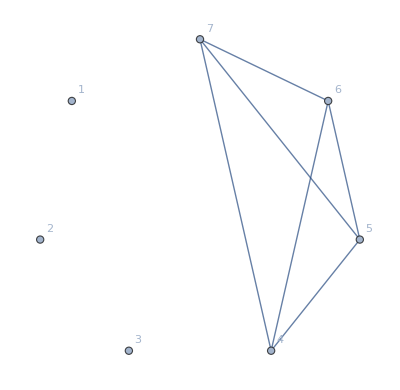
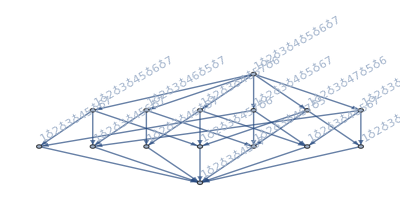
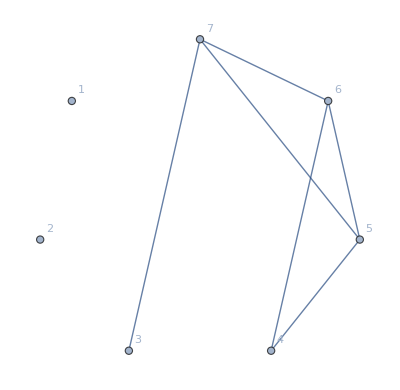
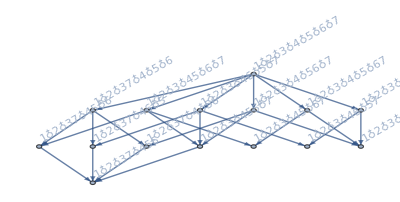
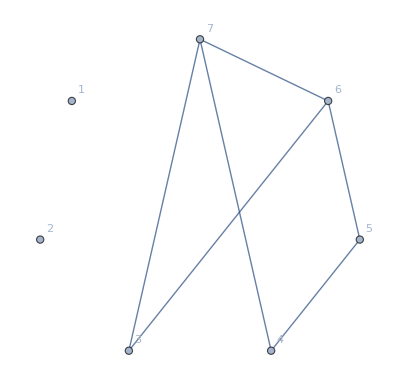
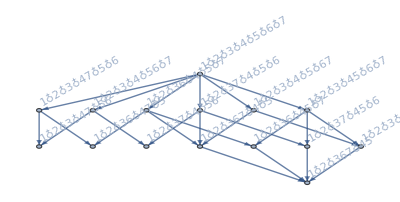
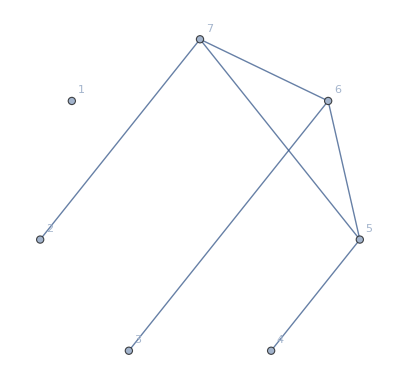
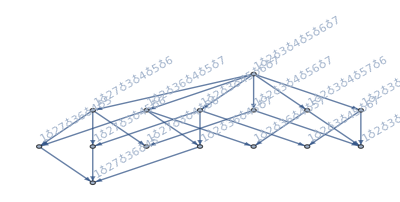

```mathematica
Map[{GraphComplement[#[[1]],VertexLabels->"Name"],Graph[FormulaGraph2[ FindFullFormula[#[[1]]]],ImageSize->{500}]}&,min7Uniq]
```